```mathematica
Solve[M1^2/(1-z)+M2^2/z==M3^2/(1-ω)+M4^2/ω,ω]
```

{{ω→(-√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))},{ω→(√((M1^2 z-M2^2 z+M2^2+M3^2 z^2-M3^2 z-M4^2 z^2+M4^2 z)^2-4 (M4^2 z^2-M4^2 z) (M1^2 (-z)+M2^2 z-M2^2))+M1^2 (-z)+M2^2 z-M2^2-M3^2 z^2+M3^2 z+M4^2 z^2-M4^2 z)/(2 (M1^2 (-z)+M2^2 z-M2^2))}}

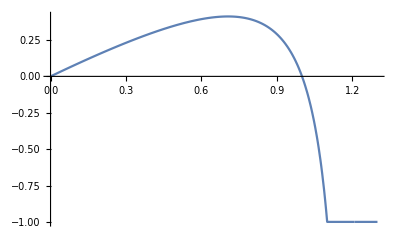

```mathematica
Plot[ω2p[ω][1.1,1.1,1,1],{ω,0,1.3}]
```

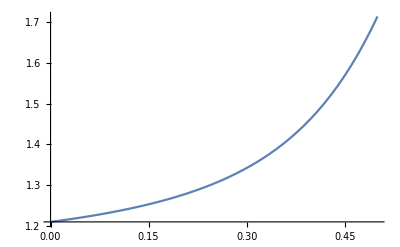

```mathematica
Plot[ω1fz[z][1.1,1.1,1,1],{z,0,0.5}]
```

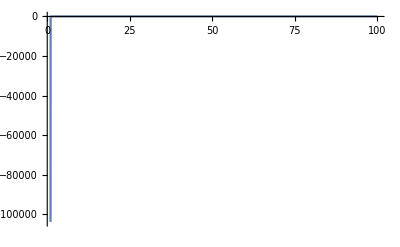

```mathematica
Plot[Sω1[ω1][1.1,1.1,1,1],{ω1,1,100}]
```

```mathematica
Sω1[1][1.1,1.1,1,1]
```

Power::infy: Infinite expression 1/0. encountered.

ComplexInfinity

```mathematica
ω/.FindMinimum[Sω1[ω][1.1,1.1,1,1],{ω,0.9}][[2]]
```

0.705917